# Noise Node discovery

## Load Nodes List

```mathematica
root = "D:/";
```

```mathematica
noisy= ToExpression//@StringSplit/@ReadList[root<>"/geo/converge_n.txt",Record];
```

## Find Noisy ones

```mathematica
noisy=noisy/.{false->False,true->True};
```

```mathematica
Tally[Total[#[[2;;]]]&/@noisy]
```

{{56+11 False,1},{1+11 False,92},{7+10 False+True,3},{7+4 False+7 True,1},{3+11 False,16},{33+False+10 True,1},{73+False+10 True,1},{63+11 False,1},{17+False+10 True,3},{10+False+10 True,4},{2+False+10 True,17},{22+11 False,2},{3+2 False+9 True,1},{7+False+10 True,4},{2+11 False,42},{3+False+10 True,8},{5+False+10 True,7},{4+11 False,18},{26+False+10 True,1},{11+False+10 True,3},{1+11 True,8},{33+11 False,2},{86+False+10 True,1},{25+False+10 True,2},{8+False+10 True,4},{21+11 False,2},{13+3 False+8 True,1},{10+11 False,6},{8+11 False,8},{71+False+10 True,2},{59+False+10 True,1},{20+11 False,3},{3+11 True,14},{51+10 False+True,1},{6+10 False+True,2},{7+11 True,6},{18+10 False+True,2},{47+11 False,3},{5+9 False+2 True,1},{7+9 False+2 True,1},{9+11 False,7},{15+11 True,6},{16+11 False,1},{5+2 False+9 True,1},{50+11 False,1},{17+11 True,5},{11+11 False,5},{8+9 False+2 True,3},{171+10 False+True,1},{5+11 True,11},{2+11 True,10},{7+3 False+8 True,1},{4+10 False+True,3},{164+False+10 True,1},{29+9 False+2 True,1},{19+2 False+9 True,1},{14+11 False,3},{4+11 True,11},{17+2 False+9 True,1},{65+10 False+True,1},{33+11 True,1},{3+10 False+True,8},{57+11 False,2},{63+10 False+True,1},{45+False+10 True,2},{5+11 False,11},{24+10 False+True,2},{19+11 False,4},{51+9 False+2 True,1},{4+False+10 True,6},{12+11 True,4},{27+10 False+True,1},{17+11 False,5},{51+False+10 True,1},{23+False+10 True,1},{49+10 False+True,1},{64+10 False+True,1},{2+9 False+2 True,2},{19+10 False+True,2},{6+11 False,6},{16+9 False+2 True,1},{37+False+10 True,2},{27+False+10 True,1},{23+10 False+True,2},{42+False+10 True,1},{10+11 True,4},{11+11 True,8},{60+False+10 True,1},{34+10 False+True,2},{31+11 False,1},{11+2 False+9 True,1},{15+8 False+3 True,1},{76+9 False+2 True,1},{25+11 True,3},{4+2 False+9 True,1},{20+False+10 True,1},{18+11 False,3},{118+11 True,1},{10+9 False+2 True,3},{11+9 False+2 True,1},{10+10 False+True,1},{9+11 True,8},{32+False+10 True,1},{121+11 True,1},{3+3 False+8 True,1},{15+11 False,4},{9+False+10 True,2},{11+10 False+True,2},{8+11 True,8},{35+11 False,2},{9+10 False+True,4},{7+11 False,3},{34+11 False,2},{36+11 False,1},{2+10 False+True,3},{22+False+10 True,3},{73+11 True,1},{6+False+10 True,1},{77+10 False+True,1},{14+False+10 True,1},{90+False+10 True,1},{25+11 False,3},{21+10 False+True,3},{20+10 False+True,1},{47+False+10 True,2},{26+11 False,1},{14+7 False+4 True,1},{18+False+10 True,1},{72+10 False+True,1},{46+False+10 True,1},{50+False+10 True,1},{6+11 True,8},{11+3 False+8 True,1},{39+11 True,2},{19+11 True,3},{20+11 True,5},{61+11 True,1},{12+11 False,3},{12+False+10 True,3},{52+10 False+True,1},{14+11 True,5},{8+2 False+9 True,1},{13+11 False,4},{29+11 True,1},{16+11 True,3},{17+10 False+True,1},{22+11 True,2},{26+11 True,3},{5+10 False+True,2},{8+10 False+True,2},{21+11 True,4},{24+False+10 True,1},{22+10 False+True,2},{24+11 False,2},{13+10 False+True,1},{18+11 True,1},{25+9 False+2 True,1},{6+2 False+9 True,1},{15+10 False+True,1},{51+11 False,1},{13+11 True,1},{12+10 False+True,1},{14+10 False+True,1},{24+9 False+2 True,1},{27+11 True,1},{5+3 False+8 True,1},{24+11 True,1},{21+9 False+2 True,1},{16+10 False+True,1},{69+10 False+True,1},{25+10 False+True,1},{35+11 True,1},{39+9 False+2 True,2},{19+9 False+2 True,1},{33+9 False+2 True,1},{71+11 True,1},{32+11 False,1},{78+9 False+2 True,1},{19+False+10 True,1},{11+8 False+3 True,2},{40+9 False+2 True,1},{28+11 True,2},{38+11 False,2},{32+11 True,1},{8+7 False+4 True,1},{48+9 False+2 True,1},{29+11 False,1},{35+9 False+2 True,2},{45+9 False+2 True,1},{8+5 False+6 True,1},{38+9 False+2 True,1},{2+7 False+4 True,1},{31+2 False+9 True,1},{39+11 False,1},{63+7 False+4 True,1},{28+11 False,1},{37+11 True,1}}

```mathematica
noisylist=Select[noisy,Last[#]==True&&#[[2]]>4&][[;;,1]]
```

{11,16,19,21,29,35,41,50,51,58,67,68,81,83,93,102,120,148,154,156,159,166,177,182,184,193,197,207,227,232,233,255,271,282,283,300,301,307,309,312,314,326,332,339,351,363,370,384,387,392,402,410,415,431,432,435,440,441,448,449,455,456,458,461,465,469,474,477,484,487,497,500,501,502,507,512,518,519,520,522,525,526,532,538,542,545,548,556,560,561,563,575,578,579,582,583,587,594,595,596,598,604,606,608,610,611,615,620,623,624,627,633,634,637,642,647,660,663,664,666,671,685,696,700,710,712,719,725,727,733,736,742,745,753,755,759,765,766,771,775,776,790,792,797,804,811,822,826,827,838,841,844,845,849,855,860,862,870,875,884,885,887,891,894,895,899,903,915,918,920,922,923,929,937,946,949,952,955,956,957,961,962,966,969,973,981,982,988,990,995,998,1000,1003,1005}

```mathematica
Length[noisy]
```

645

```mathematica
Length[noisylist]
```

194

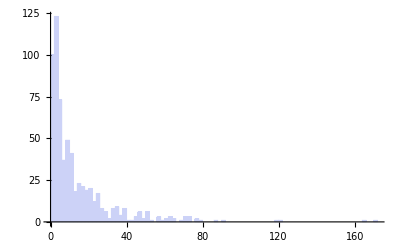

```mathematica
Histogram[#[[2]]&/@noisy,100]
```

```mathematica
noisy//TableForm;
```

## Compare with our headlist

```mathematica
corelist = ReadList[root<>"/git/posecpp/res/core_head_clusters_52.txt"]
```

{20,594,239,613,423,652,958}

```mathematica
headlist = ReadList[root<>"/git/posecpp/res/head_clusters_52.txt"]
```

{0,20,74,112,113,124,131,176,184,201,221,222,238,239,277,331,338,354,370,392,396,419,423,454,458,462,467,485,517,526,542,562,585,593,594,613,652,662,706,748,807,818,821,861,876,893,898,942,958,967,978,1004}

```mathematica
badList = {124,392,818,585,542,113}
```

{124,392,818,585,542,113}

```mathematica
Intersection[badList,noisylist]
```

{392,542}

```mathematica
Intersection[corelist,noisylist]
```

{20,423,594,613,652,958}

```mathematica
Intersection[headlist,noisylist]
```

{0,20,74,112,124,131,176,184,201,221,222,238,277,331,338,354,370,392,396,419,423,454,458,462,485,526,542,562,594,613,652,662,706,748,807,821,861,876,893,898,942,958,967,978}

```mathematica
noisy[[;;,{1,10,11,12}]]//MatrixForm;
```